# Supplementary tensors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<CTensor`
<<CITensor`
<<CIITensor`
<<CIIITensor`
<<CIIIITensor`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## ITensor

-Graphics-

The trimmed mean evaluation time is         -6
8.395 10 seconds

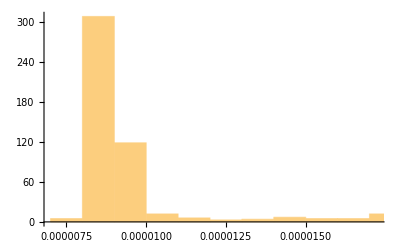

```mathematica
Table[Timing[ITensor[{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0000224725 seconds

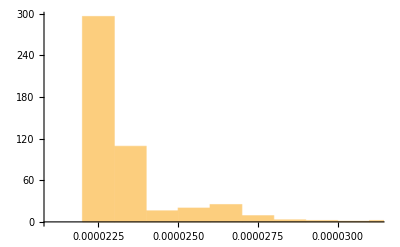

```mathematica
Table[Timing[ITensor[{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00006926 seconds

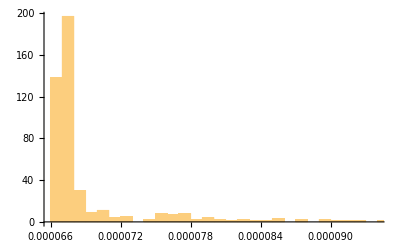

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00034503 seconds

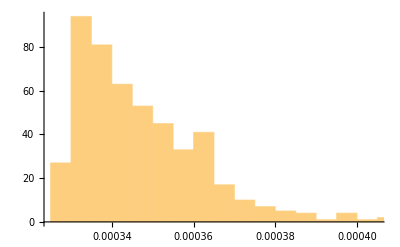

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00269198 seconds

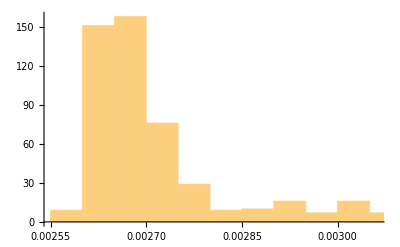

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0352169 seconds

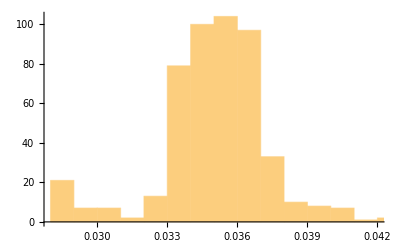

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.48845 seconds

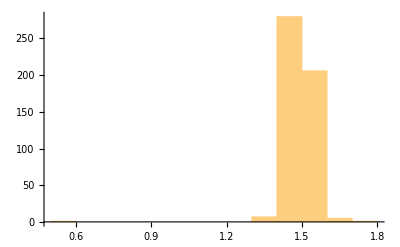

```mathematica
Table[Timing[ITensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5,r6,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CTensor

-Graphics-

The trimmed mean evaluation time is 0.0000077175 seconds

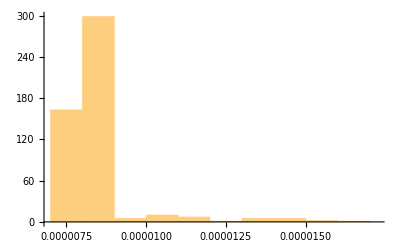

```mathematica
Table[Timing[CTensor[{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000058655 seconds

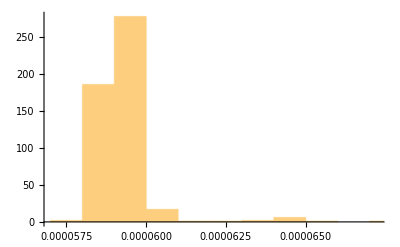

```mathematica
Table[Timing[CTensor[{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000463947 seconds

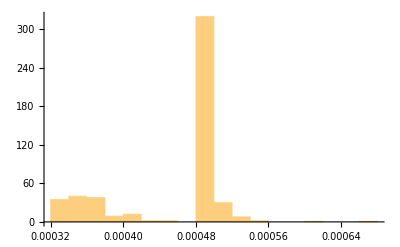

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00542608 seconds

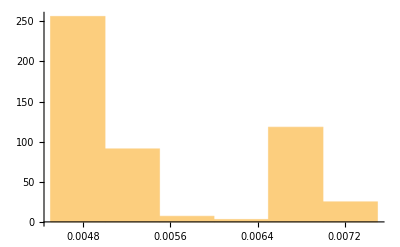

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.099464 seconds

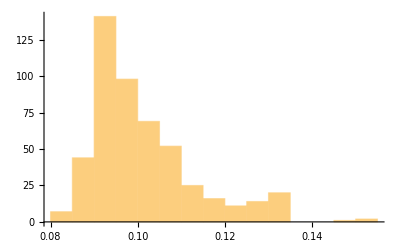

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.26699 seconds

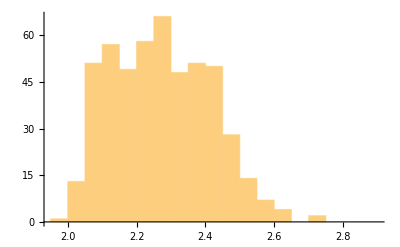

```mathematica
Table[Timing[CTensor[{r1,s1,r2,s2,r3,s3,r4,s4,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CITensor

-Graphics-

The trimmed mean evaluation time is 0.0000239125 seconds

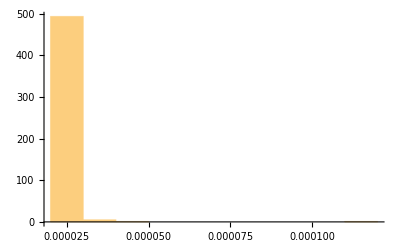

```mathematica
Table[Timing[CITensor[{μ,ν},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00008629 seconds

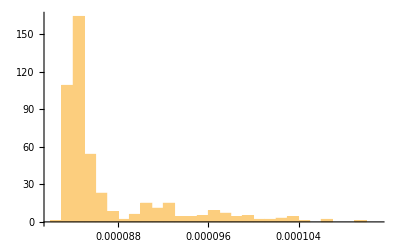

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000775557 seconds

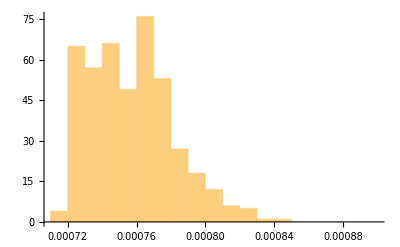

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0109196 seconds

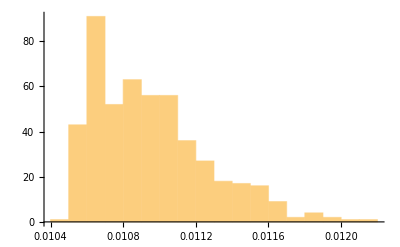

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.216967 seconds

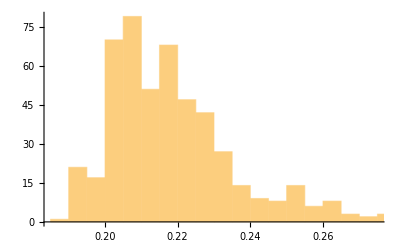

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r5,s5}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 5.90179 seconds

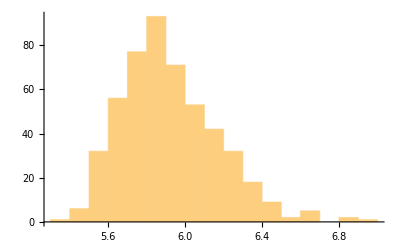

```mathematica
Table[Timing[CITensor[{μ,ν},{r1,s1,r2,s2,r3,s3,r5,s5,r6,s6}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CIITensor

-Graphics-

The trimmed mean evaluation time is 0.000063475 seconds

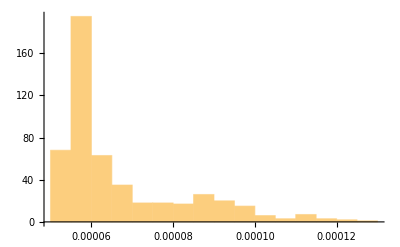

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000357945 seconds

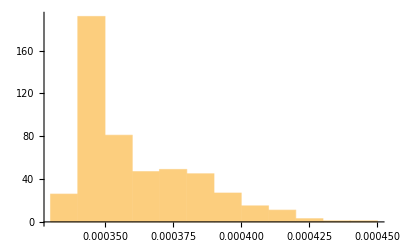

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00322368 seconds

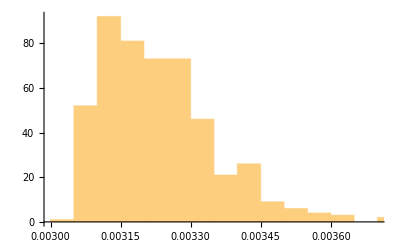

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0448911 seconds

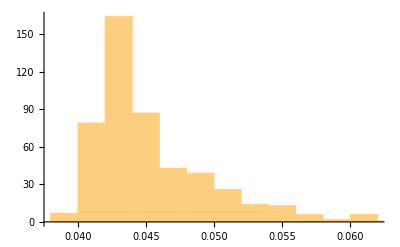

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.72978 seconds

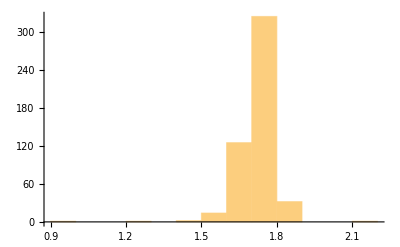

```mathematica
Table[Timing[CIITensor[{μ,ν,α,β},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CIIITensor

-Graphics-

The trimmed mean evaluation time is 0.000123073 seconds

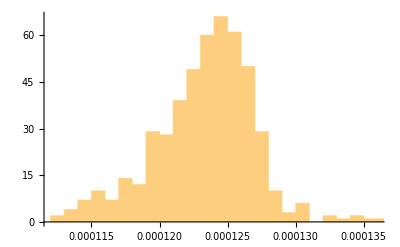

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00052459 seconds

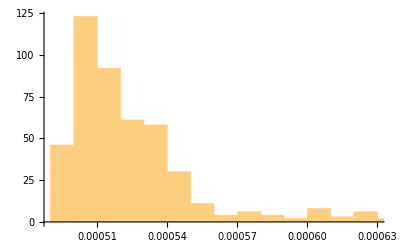

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00634697 seconds

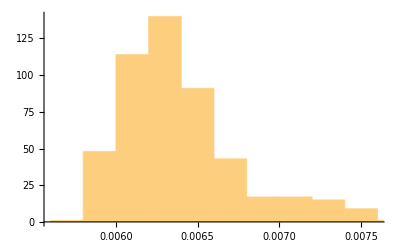

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.101317 seconds

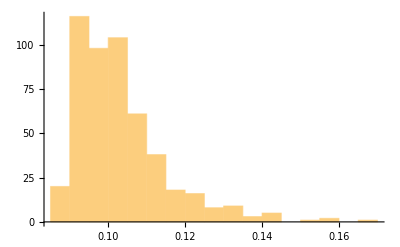

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.66493 seconds

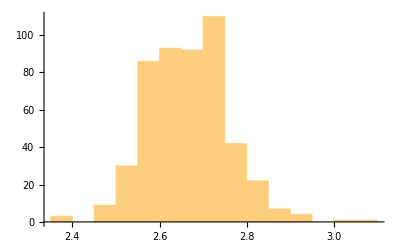

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## CIIIITensor

-Graphics-

The trimmed mean evaluation time is 0.0000793275 seconds

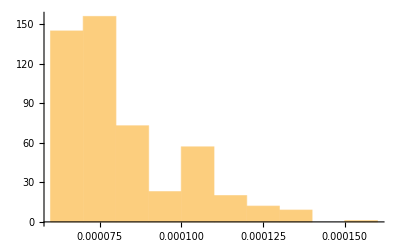

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0007856 seconds

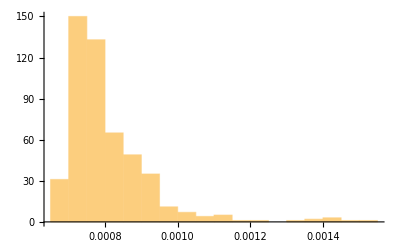

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0106057 seconds

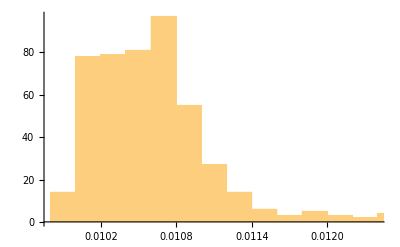

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.204228 seconds

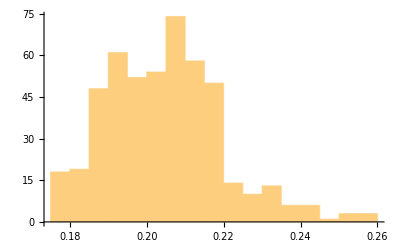

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 5.00713 seconds

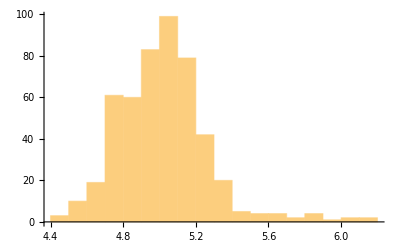

```mathematica
Table[Timing[CIIIITensor[{μ,ν,α,β,ρ,σ},{r1,s1,r2,s2,r3,s3,r4,s4}]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

# Scalar-graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Kinetic term

-Graphics-

The trimmed mean evaluation time is 0.00587889 seconds

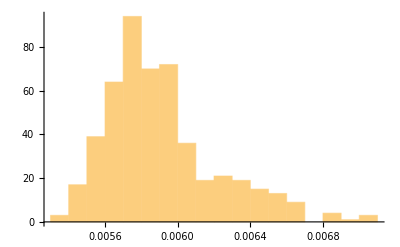

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0215196 seconds

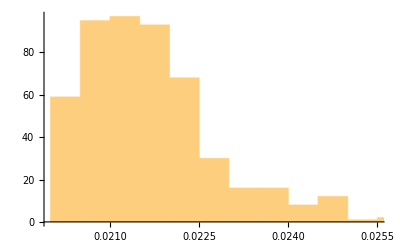

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.216192 seconds

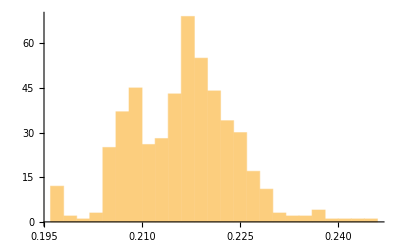

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 3.10956 seconds

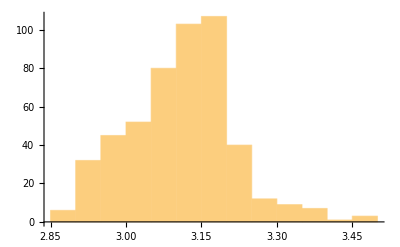

```mathematica
Table[Timing[GravitonScalarVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},p1,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## Potential term

-Graphics-

The trimmed mean evaluation time is 0.000195778 seconds

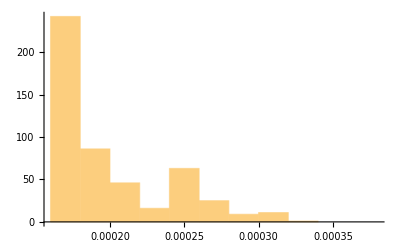

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.000563943 seconds

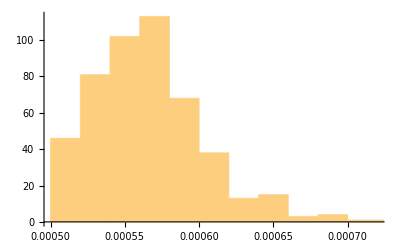

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.00541555 seconds

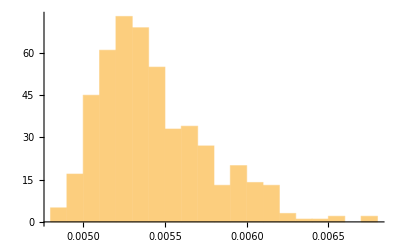

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0920115 seconds

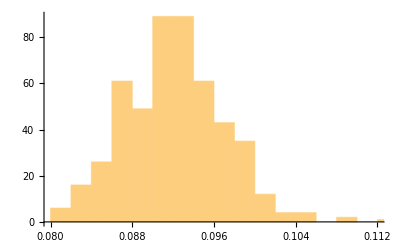

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 2.07321 seconds

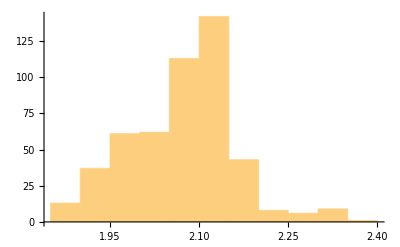

```mathematica
Table[Timing[GravitonScalarPotentialVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},λ]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

# Graviton-vector vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynGrav version 2.0

FeynGrav: FeynGravCommands print the list of all supported commands.

FeynGrav: Use '?CommandName' to see a brief description.

FeynGrav: Examples can be found in FeynGrav_Examples.nb and ArXiV:2201.06812.

Graviton-Fermion vertices are imported up to order 4 in κ.

Graviton-Gluon vertices are imported up to order 4 in κ.

Graviton-Three-Gluon vertices are imported up to order 4 in κ.

Graviton-Four-Gluon vertices are imported up to order 4 in κ.

Graviton-Quark-Gluon vertices are imported up to order 4 in κ.

Graviton-(Yang-Mills) Ghost vertices are imported up to order 4 in κ.

Graviton-Gluon-Ghost vertices are imported up to order 4 in κ.

Graviton vertices are imported up to order 3 in κ.

## Massive vectors

-Graphics-

The trimmed mean evaluation time is 0.0220552 seconds

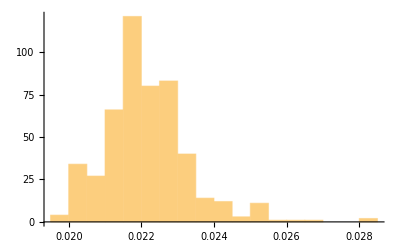

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.157797 seconds

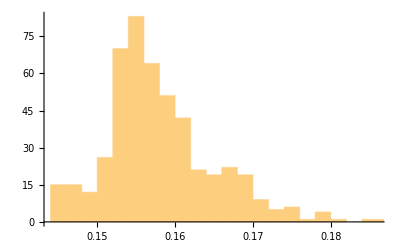

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.87156 seconds

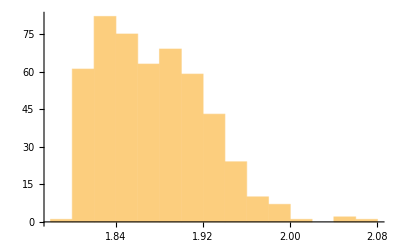

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2,μ3,ν3},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 36.371 seconds

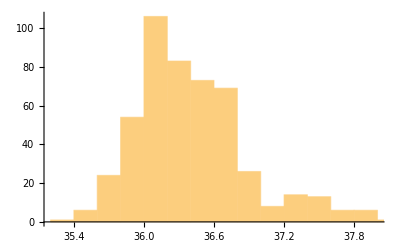

```mathematica
Table[Timing[GravitonMassiveVectorVertex[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},λ1,p1,λ2,p2,m]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## Massless vectors

-Graphics-

The trimmed mean evaluation time is 0.112661 seconds

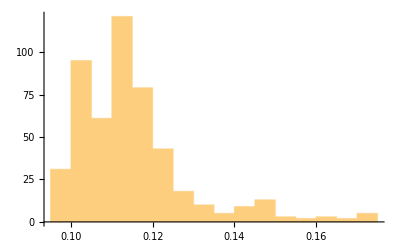

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 1.73728 seconds

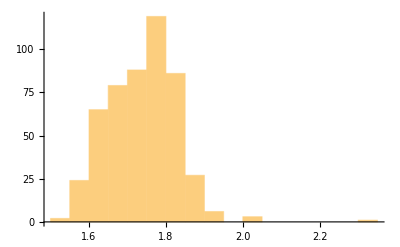

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1,μ2,ν2,k2},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 39.8028 seconds

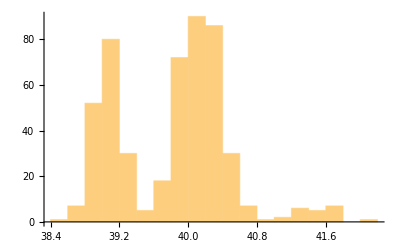

```mathematica
Table[Timing[GravitonVectorVertex[{μ1,ν1,k1,μ2,ν2,k2,μ3,ν3,k3},λ1,p1,λ2,p2,ε]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

## Ghosts

-Graphics-

The trimmed mean evaluation time is 0.00297752 seconds

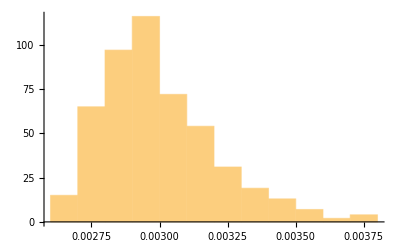

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.0211084 seconds

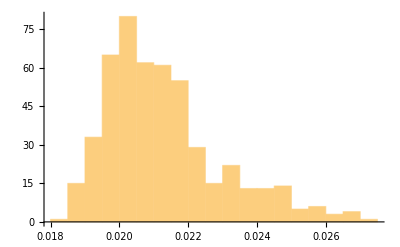

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1,r2,s2},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

-Graphics-

The trimmed mean evaluation time is 0.238343 seconds

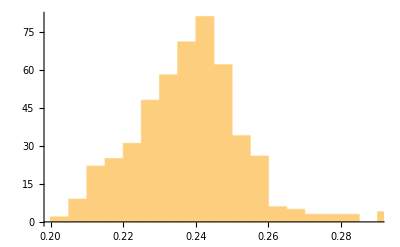

```mathematica
Table[Timing[GravitonVectorGhostVertex[{r1,s1,r2,s2,r3,s3},p1,p2]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[TrimmedMean[%%,0.1]]<>" seconds"]
Histogram[%%%]
```

# Graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

## Graviton vectors

```mathematica
Table[Timing[GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3},ε]][[1]],{n,5}];
TrimmedMean[%,0.1]
```

5.6295

```mathematica
Table[Timing[GravitonVertexb[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3},ε]][[1]],{n,5}];
TrimmedMean[%,0.1]
```

5.32983

```mathematica
GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3},ε]==GravitonVertexb[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3},ε]
```

True

```mathematica
Timing[GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3,μ4,ν4,p4},ε]][[1]]
Timing[GravitonVertexb[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3,μ4,ν4,p4},ε]][[1]]
```

331.925

194.896

```mathematica
GravitonVertex[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3,μ4,ν4,p4},ε]==GravitonVertexb[{μ1,ν1,p1,μ2,ν2,p2,μ3,ν3,p3,μ4,ν4,p4},ε]
```

True